# Motorbike net2 & net3

## Set Environment

```mathematica
ClearAll[x,y,z];
```

```mathematica
home = "Y:/pami/";workdir = "D:/git/geonb/";
```

```mathematica
SetDirectory[workdir];
```

```mathematica
Needs["Posecpp`","posecpp_network.wl"];
```

## Generate Network 2

### load raw data

```mathematica
rawData=LoadNetwork2Raw[home<>"motor_net2_raw.txt"];rawData//Dimensions
```

{80177,8}

### find best threshold

```mathematica
Module[{n = 500,v=2,a},a =ConstructNetwork2[rawData,n,v];Sow[Length[a]];
Complement[a,ConstructNetwork2[rawData,n,v-0.1]]]//Reap;
```

```mathematica
el2 = ConstructNetwork2[rawData,500,2];
```

```mathematica
g2 = Graph[el2,VertexLabels->"Name"];
```

### Node Research

```mathematica
Part[VertexList[g2],Ordering[DegreeCentrality[g2],All,Greater]]
```

{346,378,356,220,251,379,72,250,168,162,14,148,56,268,111,135,288,312,344,241,260,54,40,156,169,271,21,144,66,130,46,256,36,15,296,84,26,380,328,133,105,45,33,210,150,191,174,119,69,231,198,93,47,29,176,51,206,149,64,41,16,3,316,345,301,209,182,177,163,147,129,370,83,61,30,22,5,0,299,286,278,365,240,238,236,320,315,211,203,195,180,155,153,273,146,109,82,63,62,55,38,31,368,137,73,6,4,2,342,335,327,302,267,258,237,235,230,222,364,215,214,205,161,157,145,142,126,124,118,117,376,100,97,80,67,57,343,332,323,322,319,300,297,294,291,285,284,257,242,228,224,193,186,173,166,262,204,187,385,140,136,122,106,85,75,68,53,35,34,32,12,10,7,369,352,349,347,334,325,309,305,304,292,287,283,281,249,247,246,234,208,207,199,197,196,188,184,179,178,175,165,225,160,139,112,110,103,102,99,96,90,79,77,74,60,59,128,52,43,24,23,361,359,354,338,336,333,330,318,314,313,307,306,298,295,293,289,275,274,270,269,263,261,255,254,252,243,233,227,389,218,217,216,213,202,201,171,167,351,340,158,154,141,138,132,121,116,115,107,98,94,92,89,88,86,78,76,71,65,49,48,42,37,28,20,19,18,9}

### Export Graph

```mathematica
Export["motor_net2.txt",EdgeList[g2]]
```

motor_net2.txt

## Load Network 3

### read Edge List

```mathematica
el3=LoadNetwork3[home<>"motor_net3_el_03_01.txt"]
```

{14<->148,14<->376,15<->129,22<->136,26<->56,33<->198,47<->83,47<->144,47<->278,55<->118,61<->176,62<->99,64<->238,66<->69,72<->288,90<->199,90<->322,93<->211,93<->242,103<->284,119<->291,119<->327,130<->148,168<->260,211<->291,251<->378,257<->292,278<->299}

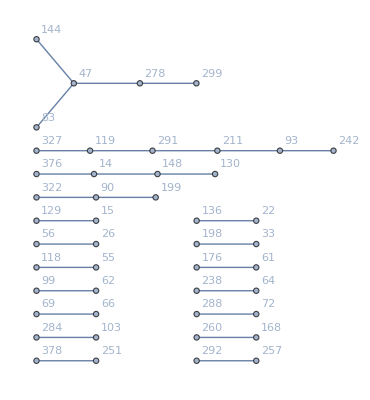

```mathematica
Graph[el3,VertexLabels->"Name"]
```

```mathematica
comp3=ConnectedComponents[Graph[el3]]
```

{{291,119,211,327,93,242},{47,83,144,278,299},{130,148,14,376},{199,90,322},{62,99},{284,103},{251,378},{136,22},{257,292},{129,15},{26,56},{238,64},{198,33},{55,118},{61,176},{66,69},{72,288},{260,168}}

## Load Global data

```mathematica
LoadGlobalData[home<>"motor_converge_x.txt",home<>"motor_converge_y.txt",home<>"motor_converge_s.txt",home<>"motor_converge_n.txt"]
```

```mathematica
cx = gx+gs/2;cy=gy+gs/2;
```

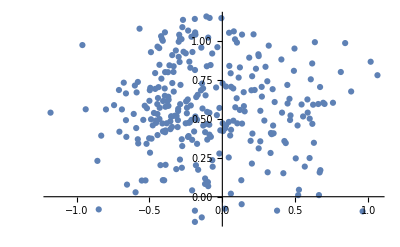

```mathematica
ListPlot[{cx[#],cy[#]}&/@Keys[gx]]
```

```mathematica
Intersection[#,Keys[gx]]&/@comp3
```

{{93,119,211,242,291,327},{47,83,144,278,299},{14,130,148,376},{90,199,322},{62,99},{103,284},{251,378},{22,136},{257,292},{15,129},{26,56},{64,238},{33,198},{55,118},{61,176},{66,69},{72,288},{168,260}}

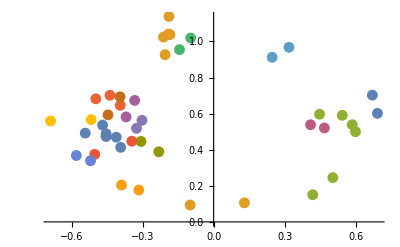

```mathematica
ListPlot[Map[{cx[#],cy[#]}&,Intersection[#,Keys[gx]]&/@comp3,{2}]]
```

```mathematica
ListPointPlot3D[Map[{cx[#],cy[#],gs[#]}&,Intersection[#,Keys[gx]]&/@comp3,{2}],Filling->Bottom,PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
Mean[gs]
```

0.417891

```mathematica
StandardDeviation[gs]
```

0.130251

```mathematica
Mean/@Map[gs[#]&,Intersection[#,Keys[gx]]&/@comp3,{2}]
```

{0.360756,0.344439,0.362133,0.38136,0.352032,0.396469,0.767527,0.3965,0.372281,0.330848,0.836027,0.366872,0.475844,0.335979,0.410927,0.412599,0.766951,0.674244}

```mathematica
Map[gs[#]&,Intersection[#,Keys[gx]]&/@comp3,{2}]
```

{{0.354006,0.361811,0.358521,0.341208,0.368141,0.380846},{0.330545,0.34774,0.342344,0.362643,0.338923},{0.374262,0.34284,0.363975,0.367456},{0.381039,0.389704,0.373338},{0.346285,0.357779},{0.39348,0.399458},{0.813928,0.721127},{0.38905,0.403949},{0.376815,0.367747},{0.334944,0.326751},{0.755648,0.916406},{0.370876,0.362867},{0.456433,0.495254},{0.333575,0.338383},{0.412666,0.409188},{0.407534,0.417664},{0.837074,0.696827},{0.785451,0.563036}}

```mathematica
sOrderByD = gs[#]&/@Part[VertexList[g2],Ordering[DegreeCentrality[g2],All,Greater]];
```

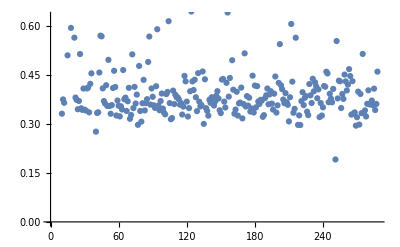

```mathematica
ListPlot[sOrderByD]
```

```mathematica
sOrderByP = gs[#]&/@Part[VertexList[g2],Ordering[PageRankCentrality[g2,0.1],All,Greater]];
```

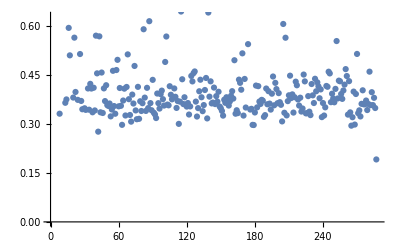

```mathematica
ListPlot[sOrderByP]
```

## Scale Slice

```mathematica
sRange ={Min[gs],Max[gs]}
```

{0.190845,1.12935}

```mathematica
FindDivisions[sRange,5]
```

{0,1/5,2/5,3/5,4/5,1,6/5}

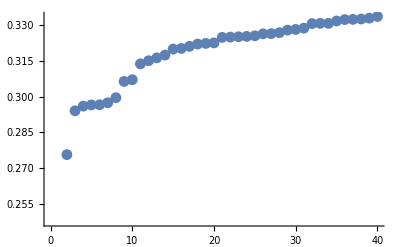

```mathematica
ListPlot[Sort[Values[gs]][[1;;40]]]
```

```mathematica
ListPointPlot3D[Map[{cx[#],cy[#],gs[#]}&,Keys[gx]],Filling->Bottom,PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
gall = Association[Map[#->{cx[#],cy[#],gs[#]}&,Keys[gx]]];
```

```mathematica
gall[0]
```

{0.111907,0.762903,0.476548}